### Initialization

#### Formatting

```mathematica
Format[ec]:=Subscript[e, c]
Format[m1]:=Subscript[m, 1]
Format[m2]:=Subscript[m, 2]
Format[ec[i_]]:=Subscript[e, i]
Format[e[i_]]:=Subscript[e, i]
Format[p[i_]]:=Subscript[p, i]
Format[a[i_]]:=Subscript[a, i]
Format[ϵ[i_]]:=Subscript[ϵ, i]
Format[ϵ[i_,j_]]:=Subscript[ϵ, i,j]
Format[e[i_,j_]]:=Subscript[e, i,j]
Format[c[i_,j_]]:=Subscript[c, i,j]
Format[e[i_,j_,k_]]:=Subscript[e, i, j ,k]
Format[p[i_,j_]]:=Subscript[p, {i|j}]
```

#### Definitions

```mathematica
h[x_]:=-x Log[2,x]-(1-x) Log[2,(1-x)]
```

```mathematica
H1[ProbDist_,d_]:=-∑_(i=0)^(d-1) ProbDist[i]Log[2,ProbDist[i]]
H2[ProbDist_,d_]:=-∑_(i=0)^(d-1) ∑_(j=0)^(d-1) ProbDist[i,j]Log[2,ProbDist[i,j]]
H3[ProbDist_,d_]:=-∑_(i=0)^(d-1) ∑_(j=0)^(d-1) ∑_(k=0)^(d-1) ProbDist[i,j,k]Log[2,ProbDist[i,j,k]]
```

```mathematica
ClockD[i_,j_,d_]:= Min[Mod[i-j,d],Mod[j-i,d]]
```

```mathematica
BiasedClockD[i_,j_,d_]:= Mod[j-i,d]
```

```mathematica
Chnl=SparseArray[{},{3,3}];
For[i=1,i<=3,i++,
For[j=1,j<=3,j++,Chnl[[i,j]]=Subscript[p, BiasedClockD[i,j,3]]]
]
Chnl//MatrixForm
Clear[i,j]
```

(p_0 | p_1 | p_2
p_2 | p_0 | p_1
p_1 | p_2 | p_0)

```mathematica
BiasedClockD[1,2,3]
```

1

```mathematica
$Assumptions={Element[k,Integers]}
```

{k∈ℤ}

#### Misc

```mathematica
$Assumptions={Element[p[i_,j_],Reals],Element[e[i_,j_,k_],Reals],Element[ϵ,Reals],Element[y,Reals],Element[n,Integers],Element[{α,β,γ},Reals]};
```

```mathematica
InEq[d_,i_]:= Conjugate[(∑_(e=0)^(d-1) p[e,0]Exp[(2π I)/d e i])](∑_(e=0)^(d-1) p[e,0]Exp[(2π I)/d e i])+Conjugate[(∑_(e=0)^(d-1) p[e,1]Exp[(2π I)/d e i])](∑_(e=0)^(d-1) p[e,1]Exp[(2π I)/d e i])
```

```mathematica
InEqO[d_,l_]:=(d-1)^2/d^4∑_(i=0)^1 Conjugate[(∑_(j=0)^(d-1) ∑_(k=0)^(d-1) e[Mod[i j+k,d],j,i]Exp[(2π I)/d k l])](∑_(j=0)^(d-1) ∑_(k=0)^(d-1) e[Mod[i j+k,d],j,i]Exp[(2π I)/d k l])
```

```mathematica
Rep1={p[e_,j_]->1/d∑_(i=0)^(d-1) P[i,j,Mod[i j+e,d]]};
Rep2={P[i_,j_,k_]->(1+e[i,j,k])/d};
```

### Joint Distribution

```mathematica
d=3;
```

```mathematica
Pa0a1[k_,l_]:=(1+b[k,l])/d^2
```

```mathematica
Pga0a1b[j_,k_,l_,i_]:=Pa0a1[k,l]∑_(m=0)^(d-1) (1+(d-1)ec[m])/d((1+(d-1)e[Mod[j+d-k+d-m,d],Mod[d-k+l,d],i])/d)
```

```mathematica
RepBiasNorm={e[0,i_,j_]->-∑_(k=1)^(d-1) e[k,i,j]};
RepBiasNorm2={e[1,i_,j_]->-∑_(k=2)^(d-1) e[k,i,j]-e[0,i,j]};
RepChannelNorm={ec[0]->-∑_(k=1)^(d-1) ec[k]};
```

#### Relevant Marginals

```mathematica
PMa0[i_]:=∑_(j=0)^(d-1) Pa0a1[i,j]
PMa1[j_]:=∑_(i=0)^(d-1) Pa0a1[i,j]
PMgcb0[n_]:=∑_(k=0)^(d-1) ∑_(l=0)^(d-1) Pga0a1b[n,k,l,0]
PMgcb1[n_]:=∑_(k=0)^(d-1) ∑_(l=0)^(d-1) Pga0a1b[n,k,l,1]
PMga0cb0[n_,k_]:=∑_(l=0)^(d-1) Pga0a1b[n,k,l,0]
PMga0cb1[n_,k_]:=∑_(l=0)^(d-1) Pga0a1b[n,k,l,1]
PMga1cb1[n_,l_]:=∑_(k=0)^(d-1) Pga0a1b[n,k,l,1]

PMga0a1cb1[n_,k_,l_]:=Pga0a1b[n,k,l,1]
```

## Correlated Inequality in d2dd

### Closed form for correlated d2dd

#### Helper Functions

```mathematica
f[j_,k_,l_,i_]:=(d-1)^2/d∑_(m=0)^(d-1) ec[m]e[Mod[j+d-k+d-m,d],Mod[d-k+l,d],i]
g[j_,k_,l_,i_]:=b[k,l](1+f[j,k,l,i])

f1[j_,k_,i_]:=1/d∑_(l=0)^(d-1) f[j,k,l,i]
g1[j_,k_,i_]:=1/d∑_(l=0)^(d-1) g[j,k,l,i]
h1[j_,k_,i_]:=f1[j,k,i]+g1[j,k,i]

f2[j_,i_]:=1/d∑_(k=0)^(d-1) f1[j,k,i]
g2[j_,i_]:=1/d∑_(k=0)^(d-1) g1[j,k,i]
h2[j_,i_]:=f2[j,i]+g2[j,i]
```

```mathematica
q[d_,s_][j_,k_,l_,i_]:=1/(d-1)∑_(m=0)^(d-1) Cos[(2π (d-m) s)/d]e[Mod[j+d-k+d-m,d],Mod[d-k+l,d],i]
```

#### Actual Inequality

```mathematica
L=-∑_(j=0)^(d-1) h2[j,0]^2+1/d∑_(j=0)^(d-1) ∑_(k=0)^(d-1) (h1[j,k,0]^2-h1[j,k,1]^2)+1/d^2∑_(j=0)^(d-1) ∑_(k=0)^(d-1) ∑_(l=0)^(d-1) (1+b[k,l])f[j,k,l,1]^2;
```

```mathematica
R=((d-1)^2∑_(m=0)^(d-1) ec[m]^2)/.RepChannelNorm//Simplify
```

8 (e_1^2+e_1 e_2+e_2^2)

```mathematica
ChannelF[i_]:=Piecewise[{{-1/(d-1),i<(d-1)/2},{1/(d-1),i>(d-1)/2}},0]
Table[ec[i],{i,0,d-1}]/.{ec[i_]->ChannelF[i]}
```

{-1/2,0,1/2}

```mathematica
T=L/R/.RepBiasNorm/.RepChannelNorm/.{ec[i_]->ChannelF[i]}//Simplify
```

1/162 (4 (1+b[0,0]) (e_(1,0,1)-e_(2,0,1))^2+4 (1+b[1,1]) (e_(1,0,1)-e_(2,0,1))^2+4 (1+b[2,2]) (e_(1,0,1)-e_(2,0,1))^2+4 (1+b[0,0]) (2 e_(1,0,1)+e_(2,0,1))^2+4 (1+b[1,1]) (2 e_(1,0,1)+e_(2,0,1))^2+4 (1+b[2,2]) (2 e_(1,0,1)+e_(2,0,1))^2+4 (1+b[0,0]) (e_(1,0,1)+2 e_(2,0,1))^2+4 (1+b[1,1]) (e_(1,0,1)+2 e_(2,0,1))^2+4 (1+b[2,2]) (e_(1,0,1)+2 e_(2,0,1))^2+4 (1+b[0,1]) (e_(1,1,1)-e_(2,1,1))^2+4 (1+b[1,2]) (e_(1,1,1)-e_(2,1,1))^2+4 (1+b[2,0]) (e_(1,1,1)-e_(2,1,1))^2+4 (1+b[0,1]) (2 e_(1,1,1)+e_(2,1,1))^2+4 (1+b[1,2]) (2 e_(1,1,1)+e_(2,1,1))^2+4 (1+b[2,0]) (2 e_(1,1,1)+e_(2,1,1))^2+4 (1+b[0,1]) (e_(1,1,1)+2 e_(2,1,1))^2+4 (1+b[1,2]) (e_(1,1,1)+2 e_(2,1,1))^2+4 (1+b[2,0]) (e_(1,1,1)+2 e_(2,1,1))^2-1/9 (3 b[0,2]+3 b[1,0]+3 b[1,1]+3 b[1,2]+3 b[2,0]+3 b[2,1]+3 b[2,2]+4 b[1,1] e_(1,0,0)-2 b[2,2] e_(1,0,0)+4 b[1,2] e_(1,1,0)-2 b[2,0] e_(1,1,0)-2 b[0,2] e_(1,2,0)+4 b[1,0] e_(1,2,0)-2 b[2,1] e_(1,2,0)+2 b[1,1] e_(2,0,0)-4 b[2,2] e_(2,0,0)+b[0,0] (3-2 e_(1,0,0)+2 e_(2,0,0))+2 b[1,2] e_(2,1,0)-4 b[2,0] e_(2,1,0)+b[0,1] (3-2 e_(1,1,0)+2 e_(2,1,0))+2 b[0,2] e_(2,2,0)+2 b[1,0] e_(2,2,0)-4 b[2,1] e_(2,2,0))^2-1/9 (3 b[0,2]+3 b[1,0]+3 b[1,1]+3 b[1,2]+3 b[2,0]+3 b[2,1]+3 b[2,2]-2 b[1,1] e_(1,0,0)-2 b[2,2] e_(1,0,0)-2 b[1,2] e_(1,1,0)-2 b[2,0] e_(1,1,0)+4 b[0,2] e_(1,2,0)-2 b[1,0] e_(1,2,0)-2 b[2,1] e_(1,2,0)-4 b[1,1] e_(2,0,0)+2 b[2,2] e_(2,0,0)+b[0,0] (3+4 e_(1,0,0)+2 e_(2,0,0))-4 b[1,2] e_(2,1,0)+2 b[2,0] e_(2,1,0)+b[0,1] (3+4 e_(1,1,0)+2 e_(2,1,0))+2 b[0,2] e_(2,2,0)-4 b[1,0] e_(2,2,0)+2 b[2,1] e_(2,2,0))^2-1/9 (3 b[0,2]+3 b[1,0]+3 b[1,1]+3 b[1,2]+3 b[2,0]+3 b[2,1]+3 b[2,2]-2 b[1,1] e_(1,0,0)+4 b[2,2] e_(1,0,0)-2 b[1,2] e_(1,1,0)+4 b[2,0] e_(1,1,0)-2 b[0,2] e_(1,2,0)-2 b[1,0] e_(1,2,0)+4 b[2,1] e_(1,2,0)+b[0,0] (3-2 e_(1,0,0)-4 e_(2,0,0))+2 b[1,1] e_(2,0,0)+2 b[2,2] e_(2,0,0)+b[0,1] (3-2 e_(1,1,0)-4 e_(2,1,0))+2 b[1,2] e_(2,1,0)+2 b[2,0] e_(2,1,0)-4 b[0,2] e_(2,2,0)+2 b[1,0] e_(2,2,0)+2 b[2,1] e_(2,2,0))^2+4 (1+b[0,2]) (e_(1,2,1)-e_(2,2,1))^2+4 (1+b[1,0]) (e_(1,2,1)-e_(2,2,1))^2+4 (1+b[2,1]) (e_(1,2,1)-e_(2,2,1))^2+4 (1+b[0,2]) (2 e_(1,2,1)+e_(2,2,1))^2+4 (1+b[1,0]) (2 e_(1,2,1)+e_(2,2,1))^2+4 (1+b[2,1]) (2 e_(1,2,1)+e_(2,2,1))^2+4 (1+b[0,2]) (e_(1,2,1)+2 e_(2,2,1))^2+4 (1+b[1,0]) (e_(1,2,1)+2 e_(2,2,1))^2+4 (1+b[2,1]) (e_(1,2,1)+2 e_(2,2,1))^2+1/3 ((-3 b[1,2]+2 e_(1,0,0)+2 e_(1,1,0)+2 b[1,2] e_(1,1,0)+2 e_(1,2,0)+b[1,1] (-3+2 e_(1,0,0)-2 e_(2,0,0))-2 e_(2,0,0)-2 e_(2,1,0)-2 b[1,2] e_(2,1,0)+b[1,0] (-3+2 e_(1,2,0)-2 e_(2,2,0))-2 e_(2,2,0))^2+(-3 b[2,2]+2 e_(1,0,0)+2 b[2,2] e_(1,0,0)+2 e_(1,1,0)+2 e_(1,2,0)-2 e_(2,0,0)-2 b[2,2] e_(2,0,0)+b[2,0] (-3+2 e_(1,1,0)-2 e_(2,1,0))-2 e_(2,1,0)+b[2,1] (-3+2 e_(1,2,0)-2 e_(2,2,0))-2 e_(2,2,0))^2+(-3 b[0,2]+2 e_(1,0,0)+2 e_(1,1,0)+2 e_(1,2,0)+2 b[0,2] e_(1,2,0)+b[0,0] (-3+2 e_(1,0,0)-2 e_(2,0,0))-2 e_(2,0,0)+b[0,1] (-3+2 e_(1,1,0)-2 e_(2,1,0))-2 e_(2,1,0)-2 e_(2,2,0)-2 b[0,2] e_(2,2,0))^2+(3 b[0,2]+4 e_(1,0,0)+4 e_(1,1,0)+4 e_(1,2,0)+4 b[0,2] e_(1,2,0)+2 e_(2,0,0)+b[0,0] (3+4 e_(1,0,0)+2 e_(2,0,0))+2 e_(2,1,0)+b[0,1] (3+4 e_(1,1,0)+2 e_(2,1,0))+2 e_(2,2,0)+2 b[0,2] e_(2,2,0))^2+(-3 b[0,2]+2 e_(1,0,0)+2 e_(1,1,0)+2 e_(1,2,0)+2 b[0,2] e_(1,2,0)+4 e_(2,0,0)+b[0,0] (-3+2 e_(1,0,0)+4 e_(2,0,0))+4 e_(2,1,0)+b[0,1] (-3+2 e_(1,1,0)+4 e_(2,1,0))+4 e_(2,2,0)+4 b[0,2] e_(2,2,0))^2+(3 b[1,2]+4 e_(1,0,0)+4 e_(1,1,0)+4 b[1,2] e_(1,1,0)+4 e_(1,2,0)+2 e_(2,0,0)+b[1,1] (3+4 e_(1,0,0)+2 e_(2,0,0))+2 e_(2,1,0)+2 b[1,2] e_(2,1,0)+2 e_(2,2,0)+b[1,0] (3+4 e_(1,2,0)+2 e_(2,2,0)))^2+(3 b[2,2]+4 e_(1,0,0)+4 b[2,2] e_(1,0,0)+4 e_(1,1,0)+4 e_(1,2,0)+2 e_(2,0,0)+2 b[2,2] e_(2,0,0)+2 e_(2,1,0)+b[2,0] (3+4 e_(1,1,0)+2 e_(2,1,0))+2 e_(2,2,0)+b[2,1] (3+4 e_(1,2,0)+2 e_(2,2,0)))^2+(-3 b[1,2]+2 e_(1,0,0)+2 e_(1,1,0)+2 b[1,2] e_(1,1,0)+2 e_(1,2,0)+4 e_(2,0,0)+b[1,1] (-3+2 e_(1,0,0)+4 e_(2,0,0))+4 e_(2,1,0)+4 b[1,2] e_(2,1,0)+4 e_(2,2,0)+b[1,0] (-3+2 e_(1,2,0)+4 e_(2,2,0)))^2+(-3 b[2,2]+2 e_(1,0,0)+2 b[2,2] e_(1,0,0)+2 e_(1,1,0)+2 e_(1,2,0)+4 e_(2,0,0)+4 b[2,2] e_(2,0,0)+4 e_(2,1,0)+b[2,0] (-3+2 e_(1,1,0)+4 e_(2,1,0))+4 e_(2,2,0)+b[2,1] (-3+2 e_(1,2,0)+4 e_(2,2,0)))^2-(-3 b[1,2]+2 e_(1,0,1)+2 e_(1,1,1)+2 b[1,2] e_(1,1,1)+2 e_(1,2,1)+b[1,1] (-3+2 e_(1,0,1)-2 e_(2,0,1))-2 e_(2,0,1)-2 e_(2,1,1)-2 b[1,2] e_(2,1,1)+b[1,0] (-3+2 e_(1,2,1)-2 e_(2,2,1))-2 e_(2,2,1))^2-(-3 b[2,2]+2 e_(1,0,1)+2 b[2,2] e_(1,0,1)+2 e_(1,1,1)+2 e_(1,2,1)-2 e_(2,0,1)-2 b[2,2] e_(2,0,1)+b[2,0] (-3+2 e_(1,1,1)-2 e_(2,1,1))-2 e_(2,1,1)+b[2,1] (-3+2 e_(1,2,1)-2 e_(2,2,1))-2 e_(2,2,1))^2-(-3 b[0,2]+2 e_(1,0,1)+2 e_(1,1,1)+2 e_(1,2,1)+2 b[0,2] e_(1,2,1)+b[0,0] (-3+2 e_(1,0,1)-2 e_(2,0,1))-2 e_(2,0,1)+b[0,1] (-3+2 e_(1,1,1)-2 e_(2,1,1))-2 e_(2,1,1)-2 e_(2,2,1)-2 b[0,2] e_(2,2,1))^2-(3 b[0,2]+4 e_(1,0,1)+4 e_(1,1,1)+4 e_(1,2,1)+4 b[0,2] e_(1,2,1)+2 e_(2,0,1)+b[0,0] (3+4 e_(1,0,1)+2 e_(2,0,1))+2 e_(2,1,1)+b[0,1] (3+4 e_(1,1,1)+2 e_(2,1,1))+2 e_(2,2,1)+2 b[0,2] e_(2,2,1))^2-(-3 b[0,2]+2 e_(1,0,1)+2 e_(1,1,1)+2 e_(1,2,1)+2 b[0,2] e_(1,2,1)+4 e_(2,0,1)+b[0,0] (-3+2 e_(1,0,1)+4 e_(2,0,1))+4 e_(2,1,1)+b[0,1] (-3+2 e_(1,1,1)+4 e_(2,1,1))+4 e_(2,2,1)+4 b[0,2] e_(2,2,1))^2-(3 b[1,2]+4 e_(1,0,1)+4 e_(1,1,1)+4 b[1,2] e_(1,1,1)+4 e_(1,2,1)+2 e_(2,0,1)+b[1,1] (3+4 e_(1,0,1)+2 e_(2,0,1))+2 e_(2,1,1)+2 b[1,2] e_(2,1,1)+2 e_(2,2,1)+b[1,0] (3+4 e_(1,2,1)+2 e_(2,2,1)))^2-(3 b[2,2]+4 e_(1,0,1)+4 b[2,2] e_(1,0,1)+4 e_(1,1,1)+4 e_(1,2,1)+2 e_(2,0,1)+2 b[2,2] e_(2,0,1)+2 e_(2,1,1)+b[2,0] (3+4 e_(1,1,1)+2 e_(2,1,1))+2 e_(2,2,1)+b[2,1] (3+4 e_(1,2,1)+2 e_(2,2,1)))^2-(-3 b[1,2]+2 e_(1,0,1)+2 e_(1,1,1)+2 b[1,2] e_(1,1,1)+2 e_(1,2,1)+4 e_(2,0,1)+b[1,1] (-3+2 e_(1,0,1)+4 e_(2,0,1))+4 e_(2,1,1)+4 b[1,2] e_(2,1,1)+4 e_(2,2,1)+b[1,0] (-3+2 e_(1,2,1)+4 e_(2,2,1)))^2-(-3 b[2,2]+2 e_(1,0,1)+2 b[2,2] e_(1,0,1)+2 e_(1,1,1)+2 e_(1,2,1)+4 e_(2,0,1)+4 b[2,2] e_(2,0,1)+4 e_(2,1,1)+b[2,0] (-3+2 e_(1,1,1)+4 e_(2,1,1))+4 e_(2,2,1)+b[2,1] (-3+2 e_(1,2,1)+4 e_(2,2,1)))^2))

### Comparing these two (in other slices)

```mathematica
PNL[a_,b_,x_,y_][i_,j_,k_]:=If[Mod[a+b,d]==Mod[x y+i x +j y+k,d],1/d,0]
PL[a_,b_,x_,y_][i_,j_,k_,l_]:=If[(a==Mod[i x +j,d]&& b==Mod[k y+l,d]),1,0]
```

```mathematica
P[a_,b_,x_,y_]:=(1-α-β) PNL[a,b,x,y][0,0,0]+ α/d(∑_(r=0)^(d-1) PL[a,b,x,y][2,r,0,Mod[d-r,d]])+ β/d^2
```

Other boxes

```mathematica
P[a_,b_,x_,y_]:=α PNL[a,b,x,y][0,0,0]+β PNL[a,b,x,y][2,1,0]+(1-α-β)1/d^2
```

```mathematica
P[a_,b_,x_,y_]:=(1-α-β) PNL[a,b,x,y][0,0,0]+ α/d(∑_(r=0)^(d-1) PL[a,b,x,y][0,r,0,Mod[d-r,d]])+ β/d(∑_(r=0)^(d-1) PL[a,b,x,y][2,r,0,Mod[d-r,d]])
```

```mathematica
P[a_,b_,x_,y_]:=(1-α-β)( (1-γ)PNL[a,b,x,y][0,0,0]+γ 1/d^2)+ α/d(∑_(r=0)^(d-1) PL[a,b,x,y][0,r,0,Mod[d-r,d]])+ β/d(∑_(r=0)^(d-1) PL[a,b,x,y][2,r,0,Mod[d-r,d]])
```

OBSERVATIONS

Notation: NS|L|L
000| 0r0r’|1r0r’| This one gives a nice inequality, but the QM line is trivial
000| 0r0r’|2r0r’| This one gives the best inequality so far, but the QM line is trivial
000| 0r0r’|1r1r’ |This one gives a not so nice inequality, but the QM line is trivial

Notation: NS|L|WN
000| 0r0r’|WN| Has a nontrivial QM line, but the inequality is always weaker
000| 0r1r’|WN| Has a nontrivial QM line, but the inequality is always weaker
000| 1r1r’|WN| Has a nontrivial QM line, the inequality is tight too, but lamer

000| 1r0r’|WN| Has a nontrivial QM line, the inequality is tight too, but only with an intersection so to speak
000| 2r0r’|WN| Has a nontrivial QM line, the inequality is tight too, but only with an intersection so to speak, but better ^^^^^^^^^
000| 2r2r’|WN| Has a nontrivial QM line, the inequality is tight too, but only with an intersection so to speak, but worse

Correlators

```mathematica
CR2[k_,x_,y_]:=(d∑_(a=0)^(d-1) P[a,Mod[d-a+k,d],x,y]-1)/(d-1)
C1A[x_]:=∑_(b=0)^1 (P[0,b,x,0]-P[1,b,x,0])
C1B[y_]:=∑_(a=0)^1 (P[a,0,0,y]-P[a,1,0,y])
```

```mathematica
∑_(a=0)^(d-1) P[a,1,1,2]//Simplify
```

1/3

```mathematica
{C1A[0],C1A[1],C1A[2],C1B[0],C1B[1],C1B[2],CR2[0,0],CR2[0,1],CR2[0,2],CR2[1,0],CR2[1,1],CR2[1,2],CR2[2,0],CR2[2,1],CR2[2,2]}//Simplify
```

{(1-β)/3,1/3 (1-2 α-β),1/3 (1-α-β),(1-β)/3,(1-β)/3,(1-β)/3,CR2[0,0],CR2[0,1],CR2[0,2],CR2[1,0],CR2[1,1],CR2[1,2],CR2[2,0],CR2[2,1],CR2[2,2]}

```mathematica
/.{b[i_,j_]->Re[(1/d+Exp[(2 π I(i+1)(j+1))/(d+1)])]ϵ}
```

```mathematica
yC1=T/.{b[i_,j_]->Im[(1/d-Exp[(2 π I i j)/(d+1)])]ϵ}/.{e[k_,i_,j_]->CR2[k,i,j]}//FullSimplify
yC2=T/.{b[i_,j_]->Re[(1/d+Exp[(2 π I(i+1)(j+1))/(d+1)])]ϵ}/.{e[k_,i_,j_]->CR2[k,i,j]}//FullSimplify
```

1/9 (-2 (-1+β)^2 (-9+ϵ^2)-2 α (-1+β) (-18+ϵ (6+ϵ))-α^2 (-27+ϵ (12+ϵ)))

1/9 (-2 (-1+β)^2 (-9+ϵ^2)-2 α (-1+β) (-18+ϵ (6+ϵ))-α^2 (-27+ϵ (12+ϵ)))

```mathematica
yC1-yC2//Simplify
```

0

3 α^2+4 α (-1+β)+2 (-1+β)^2

1/9 (-2 (-1+β)^2 (-9+ϵ^2)-2 α (-1+β) (-18+ϵ (6+ϵ))-α^2 (-27+ϵ (12+ϵ)))

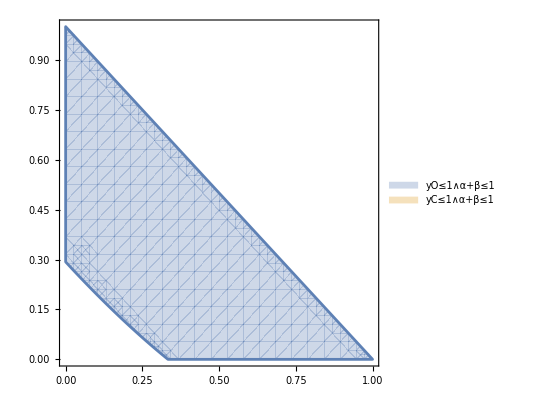

```mathematica
yO=T/.{ϵ->0}/.{e[k_,i_,j_]->CR2[k,i,j]}//Refine//Simplify
yC=T/.{b[i_,j_]->Re[(1/d+Exp[(2 π I(i+1)(j+1))/(d+1)])]ϵ}/.{e[k_,i_,j_]->CR2[k,i,j]}/.{ec[i_]->ChannelF[i]}//FullSimplify
RegionPlot[{yO<=1 && α+β<=1,yC<=1&& α+β<=1},{α,0,1},{β,0,1},PlotLegends->"Expressions"]
```

```mathematica
Manipulate[ RegionPlot[{3 α^2+4 α (-1+β)+2 (-1+β)^2<=1 && α+β<=1,1/9 (-2 (-1+β)^2 (-9+ϵ^2)-2 α (-1+β) (-18+ϵ (6+ϵ))-α^2 (-27+ϵ (12+ϵ)))<=1&& α+β<=1},{α,0,1},{β,0,1},PlotLegends->"Expressions"],{ϵ,0,1}]
```

```mathematica
Discriminant[yC-1,ϵ]
```

4/9 (2-10 α+19 α^2-18 α^3+7 α^4-12 β+34 α β-40 α^2 β+18 α^3 β+22 β^2-36 α β^2+20 α^2 β^2-16 β^3+12 α β^3+4 β^4)

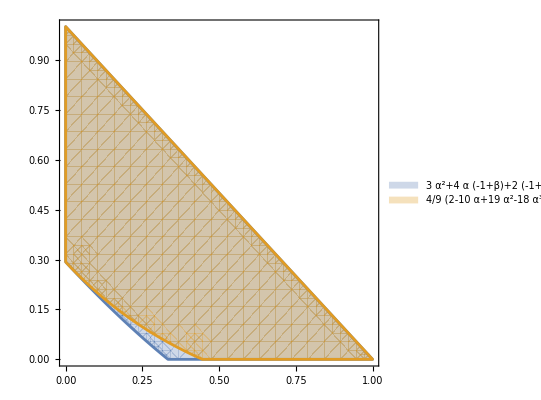

```mathematica
RegionPlot[{3 α^2+4 α (-1+β)+2 (-1+β)^2<=1 && α+β<=1,4/9 (2-10 α+19 α^2-18 α^3+7 α^4-12 β+34 α β-40 α^2 β+18 α^3 β+22 β^2-36 α β^2+20 α^2 β^2-16 β^3+12 α β^3+4 β^4)<=0&& α+β<=1},{α,0,1},{β,0,1},PlotLegends->"Expressions"]
```

### Comparing two different channels (d=4)

```mathematica
PNL[a_,b_,x_,y_][i_,j_,k_]:=If[Mod[a+b,d]==Mod[x y+i x +j y+k,d],1/d,0]
PL[a_,b_,x_,y_][i_,j_,k_,l_]:=If[(a==Mod[i x +j,d]&& b==Mod[k y+l,d]),1,0]
```

```mathematica
P[a_,b_,x_,y_]:=α PNL[a,b,x,y][0,0,0]+β PNL[a,b,x,y][0,1,0]+(1-α-β)1/d^2
```

```mathematica
P[a_,b_,x_,y_]:=(1-α-β) PNL[a,b,x,y][0,0,0]+α PL[a,b,x,y][1,0,1,0]+β PL[a,b,x,y][1,0,0,0]
```

```mathematica
CR2[k_,x_,y_]:=(d∑_(a=0)^(d-1) P[a,Mod[d-a+k,d],x,y]-1)/(d-1)
```

```mathematica
TUC=(InEqO[d,1]//Refine//ExpToTrig)/.RepBiasNorm//Expand;
```

2+3 α^2+2 α (-2+β)-2 β+β^2

TC

-1/(64 (a^2+b^2+b c+c^2+a (b+c)))(a^2 (-128+5 ϵ^2-8 β (-16+√5 ϵ)+β^2 (-64+8 √5 ϵ-5 ϵ^2)+α^2 (-256+8 √5 ϵ+5 ϵ^2)+2 α (160-4 √5 ϵ-5 ϵ^2+β (-64+8 √5 ϵ-5 ϵ^2)))+c^2 (-128+5 ϵ^2-8 β (-16+√5 ϵ)+β^2 (-64+8 √5 ϵ-5 ϵ^2)+α^2 (-256+8 √5 ϵ+5 ϵ^2)+2 α (160-4 √5 ϵ-5 ϵ^2+β (-64+8 √5 ϵ-5 ϵ^2)))+2 b^2 (-64+5 ϵ^2-8 β (-8+√5 ϵ)+β^2 (-32+8 √5 ϵ-5 ϵ^2)+α^2 (-96+8 √5 ϵ+5 ϵ^2)+2 α (64-4 √5 ϵ-5 ϵ^2+β (-32+8 √5 ϵ-5 ϵ^2)))+2 b c (-64+5 ϵ^2-8 β (-8+√5 ϵ)+β^2 (-32+8 √5 ϵ-5 ϵ^2)+α^2 (-96+8 √5 ϵ+5 ϵ^2)+2 α (64-4 √5 ϵ-5 ϵ^2+β (-32+8 √5 ϵ-5 ϵ^2)))+2 a (-32 c (2+5 α^2+2 α (-3+β)-2 β+β^2)+b (-64+5 ϵ^2-8 β (-8+√5 ϵ)+β^2 (-32+8 √5 ϵ-5 ϵ^2)+α^2 (-96+8 √5 ϵ+5 ϵ^2)+2 α (64-4 √5 ϵ-5 ϵ^2+β (-32+8 √5 ϵ-5 ϵ^2)))))

1.9+2.45279 α^2-1.55279 β+0.652786 β^2+α (-3.35279+1.30557 β)

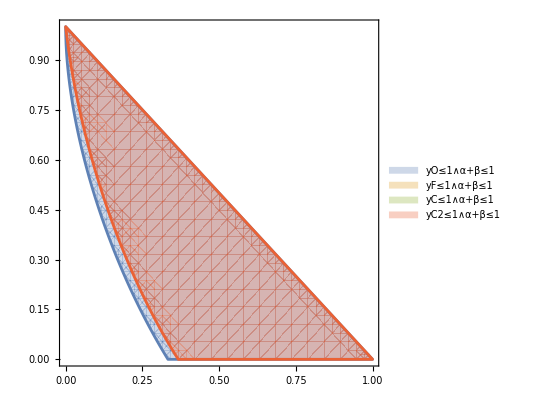

```mathematica
ChannelRep1={ec[1]->a,ec[2]->b,ec[3]->c};
ChannelRep2={ec[1]->0.1,ec[2]->0.1,ec[3]->-0.1};
yO=TUC/.{e[k_,i_,j_]->CR2[k,i,j]}//Simplify
yF=TC/.{e[k_,i_,j_]->CR2[k,i,j]}/.{ϵ->0.8}//Simplify
yC=T/.{b[i_,j_]->Re[(1/d+Exp[(2 π I(i+1)(j+1))/(d+1)])]ϵ}/.ChannelRep1/.{e[k_,i_,j_]->CR2[k,i,j]}//Simplify
yC2=T/.{b[i_,j_]->Re[(1/d+Exp[(2 π I(i+1)(j+1))/(d+1)])]ϵ}/.ChannelRep2/.{e[k_,i_,j_]->CR2[k,i,j]}/.{ϵ->0.8}//Simplify
RegionPlot[{yO<=1 && α+β<=1,yF<=1&& α+β<=1,yC<=1&& α+β<=1,yC2<=1&& α+β<=1},{α,0,1},{β,0,1},PlotLegends->"Expressions"]
```

```mathematica
d
```

3

```mathematica
Manipulate[RegionPlot[{2+3 α^2+2 α (-2+β)-2 β+β^2<=1 && α+β<=1,-1/(64 (a^2+b^2+b c+c^2+a (b+c)))(a^2 (-128+5 ϵ^2-8 β (-16+√5 ϵ)+β^2 (-64+8 √5 ϵ-5 ϵ^2)+α^2 (-256+8 √5 ϵ+5 ϵ^2)+2 α (160-4 √5 ϵ-5 ϵ^2+β (-64+8 √5 ϵ-5 ϵ^2)))+c^2 (-128+5 ϵ^2-8 β (-16+√5 ϵ)+β^2 (-64+8 √5 ϵ-5 ϵ^2)+α^2 (-256+8 √5 ϵ+5 ϵ^2)+2 α (160-4 √5 ϵ-5 ϵ^2+β (-64+8 √5 ϵ-5 ϵ^2)))+2 b^2 (-64+5 ϵ^2-8 β (-8+√5 ϵ)+β^2 (-32+8 √5 ϵ-5 ϵ^2)+α^2 (-96+8 √5 ϵ+5 ϵ^2)+2 α (64-4 √5 ϵ-5 ϵ^2+β (-32+8 √5 ϵ-5 ϵ^2)))+2 b c (-64+5 ϵ^2-8 β (-8+√5 ϵ)+β^2 (-32+8 √5 ϵ-5 ϵ^2)+α^2 (-96+8 √5 ϵ+5 ϵ^2)+2 α (64-4 √5 ϵ-5 ϵ^2+β (-32+8 √5 ϵ-5 ϵ^2)))+2 a (-32 c (2+5 α^2+2 α (-3+β)-2 β+β^2)+b (-64+5 ϵ^2-8 β (-8+√5 ϵ)+β^2 (-32+8 √5 ϵ-5 ϵ^2)+α^2 (-96+8 √5 ϵ+5 ϵ^2)+2 α (64-4 √5 ϵ-5 ϵ^2+β (-32+8 √5 ϵ-5 ϵ^2)))))<=1 && α+β<=1} ,{α,0,1},{β,0,1},PlotLegends->"Expressions"],{c,-1/(d-1),1},{a,-1/(d-1),1},{b,-1/(d-1),1},{ϵ,0,2}]
```

### Comparing two different channels (d=5)

```mathematica
PNL[a_,b_,x_,y_][i_,j_,k_]:=If[Mod[a+b,d]==Mod[x y+i x +j y+k,d],1/d,0]
PL[a_,b_,x_,y_][i_,j_,k_,l_]:=If[(a==Mod[i x +j,d]&& b==Mod[k y+l,d]),1,0]
```

```mathematica
P[a_,b_,x_,y_]:=α PNL[a,b,x,y][0,0,0]+β PNL[a,b,x,y][0,1,0]+(1-α-β)1/d^2
```

```mathematica
P[a_,b_,x_,y_]:=(1-α-β) PNL[a,b,x,y][0,0,0]+α PL[a,b,x,y][1,0,1,0]+β PL[a,b,x,y][1,0,0,0]
```

```mathematica
CR2[k_,x_,y_]:=(d∑_(a=0)^(d-1) P[a,Mod[d-a+k,d],x,y]-1)/(d-1)
```

```mathematica
TUC=(InEqO[d,1]//Refine//ExpToTrig)/.RepBiasNorm//Expand;
```

2-1/2 (-7+√5) α^2-2 β+β^2+1/2 α (-9+√5+4 β)

1/(a^2+b^2+c^2+c e+e^2+b (c+e)+a (b+c+e))(-1.97215×10^-34+1.9232 c^2+1.9232 c e+1.9232 e^2+8.85003×10^-34 c α-3.6864 c^2 α+7.4572×10^-34 e α-3.6864 c e α-4.9296 e^2 α+2.7632 c^2 α^2+2.7632 c e α^2+4.0064 e^2 α^2+5.76855×10^-34 c β-1.84 c^2 β+5.91646×10^-34 e β-1.84 c e β-2.16 e^2 β+1.8336 c^2 α β+1.8336 c e α β+2.4736 e^2 α β+0.9168 c^2 β^2+0.9168 c e β^2+1.2368 e^2 β^2+b^2 (1.9232+2.7632 α^2-1.84 β+0.9168 β^2+α (-3.6864+1.8336 β))+a^2 (1.9232+4.0064 α^2-2.16 β+1.2368 β^2+α (-4.9296+2.4736 β))+b (-1.44214×10^-33 α-1.13399×10^-33 β+e (1.9232-4.9296 α+4.0064 α^2-2.16 β+2.4736 α β+1.2368 β^2)+c (1.9232+1.52 α^2-1.52 β+0.5968 β^2+α (-2.4432+1.1936 β)))+a (1.9232 e+3.32801×10^-34 α-6.1728 e α+5.2496 e α^2+2.46519×10^-35 β-2.48 e β+3.1136 e α β+1.5568 e β^2+c (1.9232-4.9296 α+4.0064 α^2-2.16 β+2.4736 α β+1.2368 β^2)+b (1.9232+2.7632 α^2-1.84 β+0.9168 β^2+α (-3.6864+1.8336 β))))

1.9028+1.97195 α^2-1.60595 β+0.703146 β^2+α (-2.87475+1.40629 β)

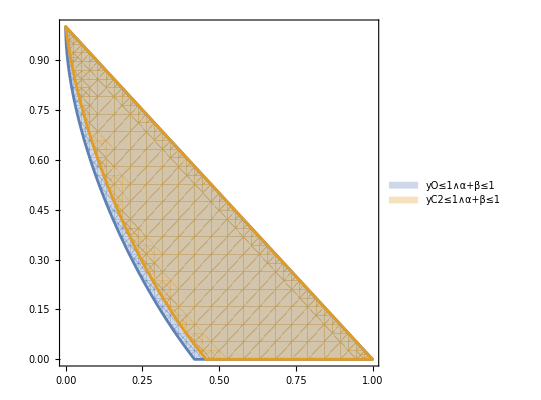

```mathematica
ChannelRep1={ec[1]->a,ec[2]->b,ec[3]->c,ec[4]->e};
ChannelRep2={ec[1]->-0.1,ec[2]->0.2,ec[3]->0.25,ec[4]->-0.1};
yO=TUC/.{e[k_,i_,j_]->CR2[k,i,j]}//Simplify
yC=T/.ChannelRep1/.{e[k_,i_,j_]->CR2[k,i,j]}/.{ϵ->0.8}//Simplify
yC2=T/.ChannelRep2/.{e[k_,i_,j_]->CR2[k,i,j]}/.{ϵ->0.9}//Simplify
RegionPlot[{yO<=1 && α+β<=1,yC2<=1&& α+β<=1},{α,0,1},{β,0,1},PlotLegends->"Expressions"]
```

```mathematica
d
```

3

```mathematica
Manipulate[RegionPlot[{2-1/2 (-7+√5) α^2-2 β+β^2+1/2 α (-9+√5+4 β)<=1 && α+β<=1,1/(a^2+b^2+c^2+c e+e^2+b (c+e)+a (b+c+e))(-1.9721522630525304*^-34+1.9232 c^2+1.9232 c e+1.9232 e^2+8.850033280448228*^-34 c α-3.6864 c^2 α+7.457200744667377*^-34 e α-3.6864 c e α-4.9296 e^2 α+2.7632 c^2 α^2+2.7632 c e α^2+4.0064 e^2 α^2+5.76854536942865*^-34 c β-1.8399999999999999 c^2 β+5.916456789157589*^-34 e β-1.8399999999999999 c e β-2.1599999999999997 e^2 β+1.8336 c^2 α β+1.8335999999999997 c e α β+2.4736000000000002 e^2 α β+0.9168 c^2 β^2+0.9167999999999998 c e β^2+1.2368000000000001 e^2 β^2+b^2 (1.9232+2.7632 α^2-1.8399999999999999 β+0.9168 β^2+α (-3.6864+1.8336 β))+a^2 (1.9232+4.0064 α^2-2.16 β+1.2368000000000001 β^2+α (-4.9296+2.4736000000000002 β))+b (-1.4421363423571621*^-33 α-1.1339875512552045*^-33 β+e (1.9232-4.9296 α+4.0064 α^2-2.1599999999999997 β+2.4736 α β+1.2368 β^2)+c (1.9232+1.52 α^2-1.5199999999999998 β+0.5967999999999999 β^2+α (-2.4432+1.1935999999999998 β)))+a (1.9232 e+3.328006943901144*^-34 α-6.1728 e α+5.2496 e α^2+2.4651903288156625*^-35 β-2.48 e β+3.1136 e α β+1.5568 e β^2+c (1.9232-4.9296 α+4.0064 α^2-2.16 β+2.4736 α β+1.2368 β^2)+b (1.9232+2.7632 α^2-1.8399999999999999 β+0.9168 β^2+α (-3.6864+1.8336 β))))<=1&& α+β<=1},{α,0,1},{β,0,1},PlotLegends->"Expressions"],{c,-1/(d-1),1},{a,-1/(d-1),1},{b,-1/(d-1),1},{e,-1/(d-1),1}]
```